```mathematica
(* Radiative Quenching *)

(* All values in atomic units *)
(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
Subscript[m, μ]=Subscript[m, p]/2;
ℏ= 1;  
(*SpeedOfLight *)
c=137 ;
(* Boltzman constant *)
Subscript[k, B] = 3.167*^-6 ;
(* Atomic unit of temperature *)
atT = 3.1577464*^5;

(* RawData format R, p, A, E, E + 1/R *)
SetDirectory[NotebookDirectory[]];
vS1RawData = Import["./s1_state.mat"][[1]];
vS2RawData = Import["./s2_state.mat"][[1]];
vP2PlusRawData = Import["./p2uPlus_state.mat"][[1]];
vP2MinusRawData = Import["./p2uMinus_state.mat"][[1]];

(* Get R, E + 1/R *)
vS1Data=Table[{vS1RawData[[i]][[1]],vS1RawData[[i]][[5]]},{i,1,Length[vS1RawData]}];
vS2Data=Table[{vS2RawData[[i]][[1]],vS2RawData[[i]][[5]]},{i,1,Length[vS2RawData]}];
vP2PlusData=Table[{vP2PlusRawData[[i]][[1]],vP2PlusRawData[[i]][[5]]},{i,1,Length[vP2PlusRawData]}];
vP2MinusData=Table[{vP2MinusRawData[[i]][[1]],vP2MinusRawData[[i]][[5]]},{i,1,Length[vP2MinusRawData]}];

lastR = vS1Data[[Length[vS1Data]]][[1]] + 1;

(* Extrapolate to from latR above to  R = 10 *)
vS1Data=Join[vS1Data,Table[{i,vS1Data[[Length[vS1Data]]][[2]]},{i,lastR,10,1}]];
vS2Data=Join[vS2Data,Table[{i,vS2Data[[Length[vS2Data]]][[2]]},{i,lastR,10,1}]];
vP2PlusData=Join[vP2PlusData,Table[{i,vP2PlusData[[Length[vP2PlusData]]][[2]]},{i,lastR,10,1}]];
vP2MinusData=Join[vP2MinusData,Table[{i,vP2MinusData[[Length[vP2MinusData]]][[2]]},{i,lastR,10,1}]];


(* 1sg state, Create a potential curve *)
Subscript[v, s1]=Interpolation[Transpose[{vS1Data[[All,1]],vS1Data[[All,2]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
Subscript[v, s2]=Interpolation[Transpose[{vS2Data[[All,1]],vS2Data[[All,2]]}], InterpolationOrder->3];
(* 2P+ state *)
Subscript[v, p2p]=Interpolation[Transpose[{vP2PlusData[[All,1]],vP2PlusData[[All,2]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
Subscript[v, p2m]=Interpolation[Transpose[{vP2MinusData[[All,1]],vP2MinusData[[All,2]]}], InterpolationOrder->3];


limit=5;


Plot[{Subscript[v, s1][r],Subscript[v, s2][r], Subscript[v, p2p][r], Subscript[v, p2m][r]},{r,0.2,limit}, PlotLabels->Automatic,AxesLabel->{"r","v[r]"},PlotStyle->{Blue,Red,Yellow,Black}, PlotLabel->"Potential Curves"]
```

-Graphics-

```mathematica
(* Compute the Dipole momement D(r) for the single value of R,
This is needed to compute the transition amplitude *)
singleDR[r_,p1_,a1_,p2_,a2_,limit_]:=Module[{lSol1,mSol1, lSol2,mSol2,norm1, norm2,dInt, ll1, ll2, mm1, mm2},
(* 1st wavefunction *)
(* x = λ, y = μ **)
lSol1=NDSolve[{(λ^2-1)L''[λ]+λ * L'[λ]+ (a1 +2 r λ -p1^2 λ^2)L[λ]==0 ,L[1.00001]==0,L'[1.00001]==1 },L[λ],{λ,1.00001,limit}][[1]];
mSol1=NDSolve[{(1-μ^2)M''[μ]-μ *M'[μ] - (a1 + p1^2 μ^2)M[μ]==0, M[0]==1,M'[0]==0}, M[μ],{μ,-.99999,.99999}][[1]];
(* 2nd wavefunction *) 
lSol2=NDSolve[{(λ^2-1)L''[λ]+λ * L'[λ]+ (a2+2 r λ -p2^2 λ^2)L[λ]==0 ,L[1.00001]==0,L'[1.00001]==1},L[λ],{λ,1.00001,limit}][[1]];
mSol2=NDSolve[{(1-μ^2)M''[μ]-μ *M'[μ] - (a2 + p2^2 μ^2)M[μ]==0, M[0]==0,M'[0]==1}, M[μ],{μ,-.99999,.99999}][[1]];

(* To evaluate NDSolve output at a single point *)
ll1[x_]:= L[λ]/. lSol1 /. λ-> x;
ll2[x_]:= L[λ]/. lSol2/. λ-> x;
mm1[y_]:= M[μ]/. mSol1 /. μ-> y;
mm2[y_]:= M[μ]/. mSol2 /. μ-> y;

(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=NIntegrate[Conjugate[(L[λ]/. lSol1)(M[μ]/. mSol1)](L[λ]/. lSol1)(M[μ]/. mSol1),{μ,-.99999,.99999},{λ,1.00001,limit}];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=NIntegrate[Conjugate[(L[λ]/. lSol2)(M[μ]/. mSol2)](L[λ]/. lSol2)(M[μ]/. mSol2),{μ,-.99999,.99999},{λ,1.00001,limit}];
dInt=(r/2)1/Sqrt[norm1+ norm2](
(mm1[-0.99999]mm2[-0.99999] + mm1[0.99999]mm2[0.99999])NIntegrate[Conjugate[(L[λ]/. lSol1)] λ(L[λ]/. lSol2),{λ,1.00001,limit}] +
NIntegrate[Conjugate[(M[μ]/. mSol1)] μ(M[μ]/. mSol2),{μ,-0.99999,0.99999}]
);
{r,(-1)dInt-r }
]

(* Get the potential difference data between state1 and state2 *)
GetInputData[state1_, state2_]:=Module[{inputData, deltaV},
Switch[state1,
"s1",
	Switch [state2,
	"p+",
		deltaV[r_]:=Abs[Subscript[v, s1][r]-Subscript[v, p2p][r]];
		inputData = Transpose[
		{vS1RawData[[All,1]],vS1RawData[[All,2]],vS1RawData[[All,3]],vP2PlusRawData[[All,2]],vP2PlusRawData[[All,3]]}],
	"p-",
		deltaV=Abs[Subscript[v, s1][r]-Subscript[v, p2m][r]];
		inputData = Transpose[
		{vS1RawData[[All,1]],vS1RawData[[All,2]],vS1RawData[[All,3]],vP2MinusRawData[[All,2]],vP2MinusRawData[[All,3]]}],
	_,Throw["Invalid State"]],
"s2", 
	Switch [state2,
	"p+",
		deltaV[r_]:=Abs[Subscript[v, s2][r]-Subscript[v, p2p][r]];
		inputData = Transpose[
		{vS2RawData[[All,1]],vS2RawData[[All,2]],vS2RawData[[All,3]],vP2PlusRawData[[All,2]],vP2PlusRawData[[All,3]]}],
	"p-",
		deltaV=Abs[Subscript[v, s2][r]-Subscript[v, p2m][r]];
		inputData = Transpose[
		{vS2RawData[[All,1]],vS2RawData[[All,2]],vS2RawData[[All,3]],vP2MinusRawData[[All,2]],vP2MinusRawData[[All,3]]}],
	_,Throw["Invalid State"]],
_,Throw["Invalid State"]];
{inputData,deltaV}
];

{inputDataS1PPlus,deltaV}=GetInputData["s1","p+"];
{inputDataS1PMinus,deltaV}=GetInputData["s1","p-"];
```

```mathematica
(*Compute the transition dipole moment *)
CalcDR[inputData_, limit_]:=Module[{allDR,dR},
allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], limit] &, inputData];
  dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
    dR
];

dRS1Plus=CalcDR[inputDataS1PPlus, limit];
dRS1PMinus=CalcDR[inputDataS1PMinus, limit];
```

```mathematica
Plot[{dRS1Plus[r],dRS1PMinus[r]},{r,.2,5},  AxesLabel->{"R (units of a_u)", "D(R) (units of a_u}"} , PlotLabels->{"2p- -> 1s+","2p+ -> 1s+"}]
```

-Graphics-

```mathematica
(* Transition Amplitude *)
aR[R_,state1_, state2_, limit_]:=Module[{inputData, deltaV,dR, dV},
{inputData, dV}=GetInputData[state1,state2];
dR =CalcDR[inputData, limit];
deltaV[r_]:=dV[r];
4/3(dR[R])^2(deltaV[R])^3/c^3 
];
```

```mathematica
(* Energy  Range, for temperatures from 0K - 2K 
Subscript[k, B] T = 1/2 m v^2 = E, T in Kelvin  *)

energies = Interpolation[ Table[Subscript[k, B] atT  T, {T,0,2,.1}],InterpolationOrder->3];

Subscript[k, ar][x_]:=Sqrt[2 Subscript[m, μ] (energies[x] - Subscript[v, s1][10])];
Subscript[v, s1][10]
Subscript[k, ar][5]
Plot[{Subscript[k, ar][r],energies[r] },{r,1,5}, PlotLabels->Automatic]
```

InterpolatingFunction[…]

-2.00134

66.3995

-Graphics-

```mathematica
solF[j_]:=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s1][r]+j^2/r^2)ff[r],ff,{r,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]][[1]];
```

```mathematica
(* 2D Schrodinger equation, m is a paramete #  (called J in 3D case),
grab the lowest eigenvalue, i.e. value of k *)
solS1J=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s1][r]+#^2/r^2)ff[r],ff,{r,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]][[1]]&;
(*solS2J[j_]:=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s2][r]+j^2/r^2)ff[r],ff[r],{r,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];*)
(*  1S state *)
allS1Js = Map[solS1J, Table[j,{j,0,2}]];
allS1Js //MatrixForm
```

(-5.11118 | InterpolatingFunction[…]
-6.33783 | InterpolatingFunction[…]
-8.4653 | InterpolatingFunction[…])

```mathematica
allS1Ks =  allS1Js[[All,1]];
allS1JFunc = allS1Js[[All,2]] ;
Subscript[k, A]=allS1Ks (* j = 0,1,2 *)


fS1[j_,x_]:=allS1JFunc[[j]][x];
```

{-5.11118,-6.33783,-8.4653}

```mathematica
(* Calculate the integral *)

Subscript[η, s1pp][j_] := NIntegrate[(Abs[ allS1JFunc[[j]][x]])^2 aR[x,"s1", "p+", limit],{x,.2,limit}];
ScientificForm[Subscript[η, s1pp][1]]
```

(8.0765×10^-4)

```mathematica
Subscript[η, s1pm][j_] := NIntegrate[(Abs[ allS1JFunc[[j]][x] ])^2 aR[x,"s1", "p-", limit],{x,.2,limit}];
Subscript[η, s2pp][j_] := NIntegrate[(Abs[allS2JFunc[[j]][x]])^2 aR[x,"s2", "p+", limit],{x,.2,limit}];
Subscript[η, s2pm][j_] := NIntegrate[(Abs[allS2JFunc[[j]][x]])^2 aR[x,"s2", "p-", limit],{x,.2,limit}];
```

tt

-5.11118

60.6173

InterpolatingFunction::dmval: Input value {0.100039} lies outside the range of data in the interpolating function. Extrapolation will be used.

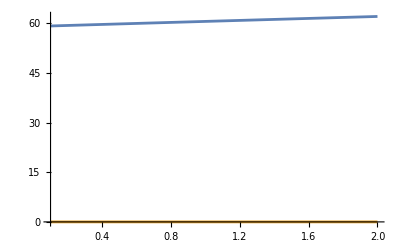

{-5.11118,-6.33783,-8.4653}

```mathematica
(* Cross Section *)

(*σ=Pi/Subscript[k, A]^2 Sum[1-Exp[-4 Subscript[η, s1pp][j]],{j,0,1}];*)
Remove[σ];
tt
σ[r_]:=Pi/(Subscript[k, ar][r])^2 Sum[1-Exp[-4 Subscript[η, s1pp][j]],{j,0,1}];
Subscript[k, A]
Subscript[k, ar][1]
Plot[{Subscript[k, ar][r],σ[r]},{r,0.1,2}]
allS1Ks
```